```mathematica
Clear[ρ,Fd,Fg,s,t]
ρ[s,t]=ρ0 Exp[-s[t]/H0]

s0 = 39000;
v0 = 0;
ρ0 = 1.2;
H0 = 7000;
g=-9.81;
m=127;
c=Cd A;

Fd[s_,t_]=-Sign[s'[t]]/2 Cd*A*ρ[s,t]*s'[t]^2;
Fg[s_,t_]=m g;

tmax = 200;
sol[t_]=s[t]/.First[NDSolve[{s''[t]==Fd[s,t]/m+Fg[s,t]/m,s[0]==s0,s'[0]==v0},s,{t,0,tmax}]]
```

1.2 ⅇ^(-s[t]/7000)

InterpolatingFunction[…][t]

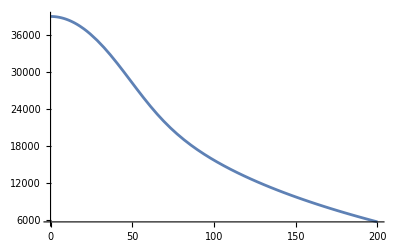

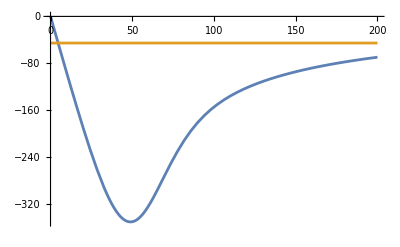

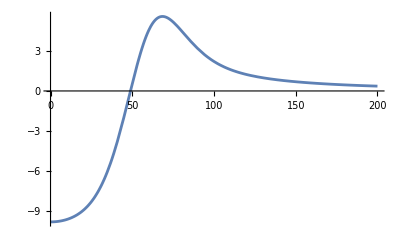

```mathematica
Plot[sol[t],{t,0,tmax},PlotRange->Full]
Plot[{sol'[t],-√((2 m Abs[g])/(ρ0 Cd A))},{t,10^-2,tmax},PlotRange->Full]
Plot[sol''[t],{t,10^-2,tmax},PlotRange->Full]
```

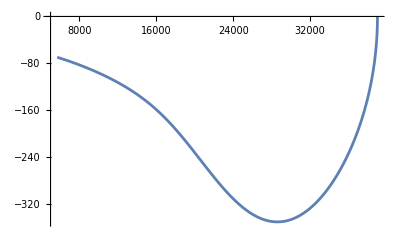

```mathematica
altitude= Table[sol[t],{t,Subdivide[0,tmax,500]}];
velocity= Table[sol'[t],{t,Subdivide[0,tmax,500]}];
ListPlot[{altitude,velocity}ᵀ,PlotRange->Full,Joined->True]
```

```mathematica
√((2 80 Abs[9.81])/(1.225 0.47 0.1))
```

165.112